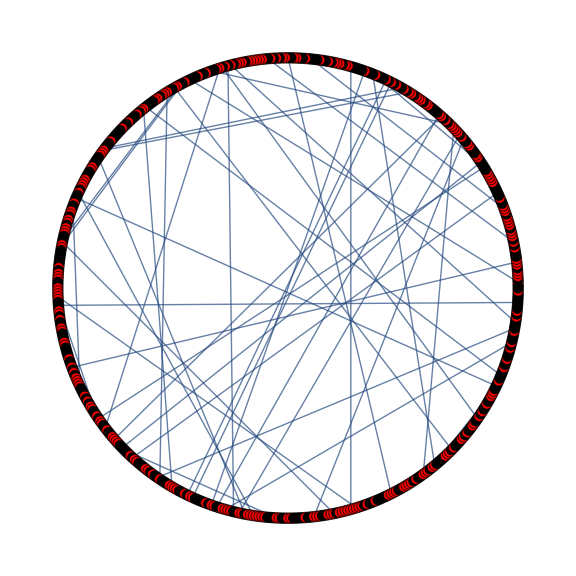

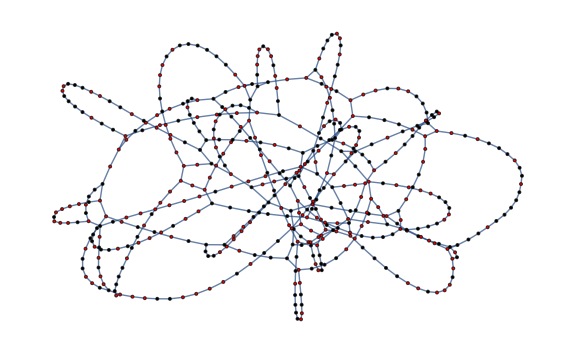

None

```mathematica
export=False;
(* Set the function describing the position of vertices *)
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2 Pi/n u],b Sin[2 Pi/n u]},{u,1,n}]

(* Import graph data from target directory *)
graph=Import[
"/Users/jeepee/Documents/Cpp_trade/cpp-course/swn-Ising/swn/connections.mma.list"];

(* Parse the imported data *)
len=ToExpression@graph[[1]][[1]];
connectionTable=ToExpression@graph[[2]][[1]];
workingDirectory=ToString@graph[[3]][[1]];
vStyleRules=None;
If[Length@graph≥4,
vStyleRules=ToExpression@graph[[4]][[1]],None];

(* Plot graphs *)
g1=Graph[connectionTable,
VertexCoordinates->ellipseLayout[len,{1,1}],
ImageSize->Large,VertexStyle->vStyleRules]
g2=Graph[connectionTable,
ImageSize->Large,VertexStyle->vStyleRules]

(* Export graphs if permitted *)
If[export==True,
(Export[workingDirectory<>"/fig/circleGraph.png",g1];
Export[workingDirectory<>"/fig/automaticGraph.png",g2];),
None]
```

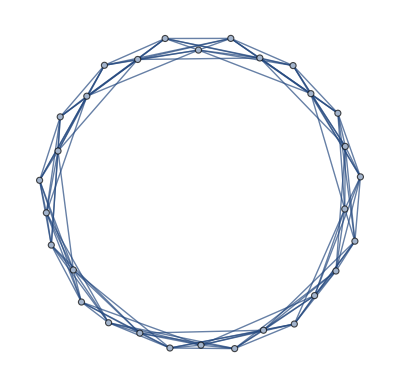

120

```mathematica
g=RandomGraph[WattsStrogatzGraphDistribution[30,0,4]]
EdgeCount@g
```

```mathematica
f=CDF[ NormalDistribution[],#]&;
g=CDF[UniformDistribution[],#]&;
NIntegrate[x(Integrate[g[x1],{x1,0,x}])^10,{x,0,1}]
```

Integrate::pwrl: Unable to prove that integration limits {0, x} are real. Adding assumptions may help.

0.0000443892

```mathematica
Plot[(NIntegrate[g[x1],{x1,0,0.8}])^n,{n,1,10}]
```

Plot::plln: Limiting value ， in {n, 1\ ，\ 1, 10} is not a machine-sized real number.

Plot[NIntegrate[g[x1],{x1,0,0.8}]^n,{n,1 ， 1,10}]

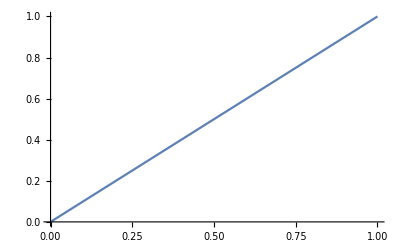

```mathematica
Plot[g[x],{x,0,1}]
```